## Empirical approaches old Ch 8 new Ch 9

```mathematica
SetDirectory[NotebookDirectory[]];Get["Packages\\TextbookFigurePreamble.wl"] (* loads libraries, textbook stylings and defines txbExport *)
```

Global::txbDraftFigurePath

```mathematica
Context[txbDraftFigurePath]
```

TextbookStylings`

```mathematica
figMOSI
```

figMOSI

```mathematica
countMOSI = {89,89,89,89,89,55,74,89,55,89,53,54,34,89,55,55,34,55,21,55,34,41,55,88,36,29,42,21,18,34,55,89,55,89,55,89,76,89,83,55,55,55,78,55,88,89,89,144,89,89,93,55,89,89,88,55,89,89,68,89,89,34,55,89,76,34,54,89,144,55,55,88,55,89,73,89,68,89,88,86,90,143,110,89,143,142,144,144,89,89,89,89,34,21,79,55,88,34,54,47,48,50,89,54,89,59,55,68,55,55,55,76,89,55,55,47,89,55,89,33,35,43,57,20,19,55,40,89,89,47,55,34,53,84,89,89,89,89,55,34,34,34,54,55,55,55,55,89,89,55,55,55,55,55,55,55,87,123,33,55,89,55,55,143,89,55,53,89,89,76,54,21,33,47,32,55,49,89,76,55,55,89,68,55,89,34,55,56,57,89,53,89,55,88,55,55,55,55,55,34,55,55,55,55,34,34,55,144,76,34,55,89,55,89,34,55,55,55,76,144,19,57,21,34,55,89,89,68,89,89,55,89,88,89,88,50,89,89,89,55,75,88,55,34,89,89,54,89,89,89,89,55,55,55,55,34,34,144,54,89,88,55,55,89,89,55,89,55,55,55,86,89,54,86,89,55,73,89,80,34,55,89,34,89,53,89,55,89,89,55,34,55,34,55,55,55,68,89,55,34,89,55,68,77,47,55,55,55,55,55,54,47,89,55,34,54,55,88,34,55,47,55,55,34,55,55,55,55,55,74,89,54,89,55,55,55,55,55,55,55,55,42,55,54,55,55,68,55,55,55,54,55,55,55,47,55,55,55,55,68,55,55,55,47,55,55,88,50,89,112,89,89,89,89,89,55,68,55,55,55,55,55,55,62,44,29,55,89,89,55,55,34,55,34,34,34,89,75,87,52,55,55,55,56,55,34,55,34,53,34,36,21,55,34,21,34,20,34,21,25,34,55,21,20,26,13,21,34,55,36,55,34,55,47,55,49,35,34,47,34,55,55,89,55,57,34,55,55,55,34,55,55,42,55,55,22,34,55,47,21,34,55,89,34,34,55,34,55,45,55,42,55,54,54,89,68,55,90,89,89,89,55,55,55,55,21,47,55,21,34,29,48,55,55,55,42,34,34,34,47,55,34,34,29,55,34,55,21,21,29,33,13,34,55,55,28,34,34,54,55,55,55,55,34,21,21,21,34,34,34,34,55,54,34,34,34,34,34,34,55,76,19,35,55,34,34,88,55,34,35,55,55,47,36,13,21,29,34,32,56,47,36,34,55,42,34,55,21,34,54,56,34,55,34,34,34,34,34,21,34,34,34,34,21,21,34,47,21,34,55,34,55,34,34,34,47,89,18,34,13,21,34,55,55,42,55,55,34,54,55,55,55,55,55,55,34,48,34,21,55,56,35,55,55,55,55,34,34,36,34,21,21,89,34,55,55,34,34,55,55,55,34,34,34,56,54,34,55,56,34,55,55,68,21,34,55,21,55,34,55,55,34,21,34,34,34,34,42,54,34,21,54,34,56,29,34,34,34,34,34,34,29,55,34,21,34,34,55,21,34,29,34,34,34,34,34,34,34,46,55,34,55,36,35,38,37,34,34,34,34,27,34,34,34,33,42,34,34,34,34,34,34,34,29,34,34,34,34,42,34,36,34,29,34,34,55,31,55,69,55,55,55,55,55,34,42,34,34,34,34,34,34,31,28,34,54,55,34,34,21,34,21,21,21,55,47,52,31};
```

```mathematica
fType[x_] := Which[
MemberQ[{13,21,34,55,89,144}-1,x],"Fibonacci ±1",
MemberQ[{13,21,34,55,89,144}+1,x],"Fibonacci ±1",
MemberQ[{1,4,5,9,14,23,37,60,97},x],"F4",
MemberQ[{1,3,4,7,11,18,29,47,76,123},x],"Lucas",
MemberQ[{2,4,6,10,16,26,42,68,110},x],"Fibonacci x2",
MemberQ[{1,2,3,5,8,13,21,34,55,89,144},x],"Fibonacci",
True,"Other"
];

f6Palette = Append[jStyle["ParastichyColour"],6->jStyle["CylinderColour"]];
f6Keys = {"Fibonacci","Fibonacci x2","Lucas","F4","Fibonacci ±1","Other"};
fColourPalette = AssociationThread[f6Keys,Values[f6Palette]];
fColourPalette["F4"] = Directive[FaceForm[fColourPalette["F4"]],EdgeForm[{Black}]];
```

```mathematica
bar[{spirals_,observed_}] := Module[{},
barColour = fColourPalette[fType[spirals]];
{barColour,Rectangle[ {spirals-0.45,0},{spirals+0.45,observed}]}
];

fsize[str_,n_] := Style[str,FontFamily-> jStyle["FontFamily"],FontSize->n];
fxsize[str_] := fsize[str,12];
alabel =Map[fsize[#,12]&,{"Parastichy number","Count"}];
imagePadding = 42*{ {1,1},{1,0.1}};
imageSize = 300;
legend =SwatchLegend[
Values[fColourPalette],Map[fxsize,Keys[fColourPalette]]];
g1 =Graphics[
{Map[bar,Tally[countMOSI]]},
Axes->True,
FrameTicks->{ {{100,200},None},{{21,34,55,89,144},None}},AxesOrigin->{1,0},AspectRatio->1,
FrameLabel->alabel,Frame->True,PlotRangeClipping->True,ImagePadding->imagePadding,
LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->12,FontColor->Black],
PlotLabel->fxsize@"All",
ImageSize->imageSize
,PlotRange->{{0,150},{0,250}}];
g2 =Graphics[
{Map[bar,Tally[countMOSI]]},
Axes->True,
FrameTicks->{{{5,10,15,20},None},{{21,34,55,89,144}, None}},AxesOrigin->{20,0},AspectRatio->1,
FrameLabel->alabel,Frame->True,PlotRangeClipping->True,ImagePadding->imagePadding,
LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->12,FontColor->Black],
PlotLabel->fxsize@"Detail",
ImageSize->imageSize,
PlotRange->{{20,94},{0,25}}];


txbMOSIplines := Grid[{{Legended[g1,Placed[legend,{0.8,Center}]]},{g2}}]
```

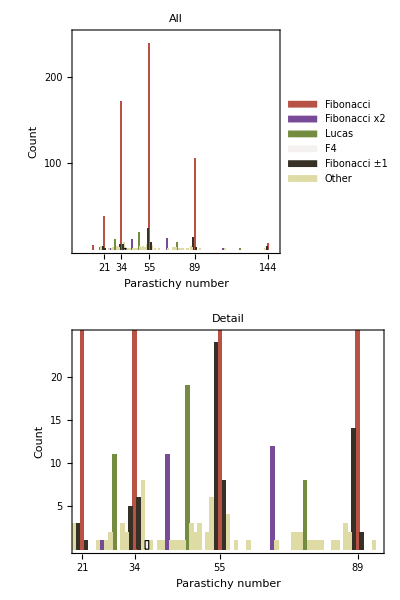

```mathematica
txbExport[txbMOSIplines]
```

```mathematica
fierz = <| "8:13" -> 5838,"10:16"->69,"7:11"-> 20,"9:15"-> 9,"9:14"-> 3,"7:12"-> 3,"8:12"->5,"6:11"->1,"9:13"->2,"7:10"->1,"Irregular"->49|>
```

<|8:13→5838,10:16→69,7:11→20,9:15→9,9:14→3,7:12→3,8:12→5,6:11→1,9:13→2,7:10→1,Irregular→49|>

```mathematica
(*
SetDirectory[NotebookDirectory[]];
cfJean = Import["../R\\Counts-Ftype.csv","Dataset","HeaderLines"->1];
SetDirectory["Draft Figures"];
cfJean = cfJean[Select[#Ftype != "Any" && #Observer != "Public"&]] 
Normal@cfJean[All,{"Observer","Ftype","Observed"}]
*)
```

```mathematica
dsJean = Dataset@{<|"Observer"->"MOSI","Ftype"->"Fibonacci","Observed"->565|>,<|"Observer"->"MOSI","Ftype"->"Fibonacci x2","Observed"->25|>,<|"Observer"->"MOSI","Ftype"->"Lucas","Observed"->41|>,<|"Observer"->"MOSI","Ftype"->"F4","Observed"->1|>,<|"Observer"->"MOSI","Ftype"->"Fibonacci -1","Observed"->49|>,<|"Observer"->"MOSI","Ftype"->"Fibonacci +1","Observed"->17|>,<|"Observer"->"MOSI","Ftype"->"Other","Observed"->70|>,<|"Observer"->"Schoute","Ftype"->"Fibonacci","Observed"->262|>,<|"Observer"->"Schoute","Ftype"->"Fibonacci -1","Observed"->0|>,<|"Observer"->"Schoute","Ftype"->"Lucas","Observed"->46|>,<|"Observer"->"Schoute","Ftype"->"F4","Observed"->2|>,<|"Observer"->"Schoute","Ftype"->"Fibonacci x2","Observed"->9|>,<|"Observer"->"Schoute","Ftype"->"Other","Observed"->0|>,<|"Observer"->"Schoute","Ftype"->"Fibonacci +1","Observed"->0|>,<|"Observer"->"Weisse","Ftype"->"Other","Observed"->0|>,<|"Observer"->"Weisse","Ftype"->"Fibonacci +1","Observed"->0|>,<|"Observer"->"Weisse","Ftype"->"Fibonacci","Observed"->133|>,<|"Observer"->"Weisse","Ftype"->"F4","Observed"->0|>,<|"Observer"->"Weisse","Ftype"->"Fibonacci x2","Observed"->1|>,<|"Observer"->"Weisse","Ftype"->"Lucas","Observed"->6|>,<|"Observer"->"Weisse","Ftype"->"Fibonacci -1","Observed"->0|>}
```

```mathematica
fClass = {"Fibonacci","Fibonacci x2","Lucas","F4","Fibonacci -1","Fibonacci +1","Other"};
fClass6 = {"Fibonacci","Fibonacci x2","Lucas","F4","Fibonacci +-1","Other"};
authors = Reverse@{"MOSI","Schoute","Weisse"};
fData[author_] := Module[{},
aData = dsJean[Select[#Observer==author&]];
fofType[type_] := First@Normal@aData[Select[#Ftype==type &],"Observed"];
counts  = AssociationThread[fClass,Map[fofType,fClass]];
AppendTo[counts,"Fibonacci +-1"-> counts["Fibonacci +1"]+counts["Fibonacci -1"]];
counts6 = KeyTake[counts,fClass6];
fractions6 = Reverse@Map[#/Total[counts6]&,counts6];
fractions6
];
sbd =Map[Values@*fData,authors]
```

{{0,0,0,3/70,1/140,19/20},{0,0,2/319,46/319,9/319,262/319},{35/384,11/128,1/768,41/768,25/768,565/768}}

```mathematica
barlegend =SwatchLegend[Values[fColourPalette],Keys[fColourPalette],LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.05]]];
authorStyle = Map[Style[#,Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.05]]]&,authors];

Ch7cfJean := Legended[
BarChart[
sbd
,ChartLayout->"Stacked"
,ChartStyle->Reverse@Values@fColourPalette
,ChartLabels->{Placed[authorStyle,Axis],{""}}
,BarSpacing->{0,0.5}
,PlotRange->{{0.5,3.5},{-0.3,1.2}}
],
Placed[barlegend,{{1.4,1/2},{1,1/2}}]]
```

```mathematica
jExport[Ch7cfJean]
```

-Graphics-

```mathematica
bractWorksheet = Import["../..\\R\\Worksheet.csv","Dataset",HeaderLines->1];
bractCount = Normal@bractWorksheet[All,"Bract.count"] /. "NA"->Nothing[]

Ch7BractCount := Show[
Histogram[bractCount,{1},
LabelStyle->Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.05]],
AxesLabel->Map[Style[#,Directive[FontFamily-> jStyle["FontFamily"],FontSize->Scaled[0.05]]]&,
{"Bract count","Observed"}]
,ChartStyle->f6Palette[2]
]
,Graphics[{f6Palette[1],Map[InfiniteLine[{#,0},{0,1}]&,0.5+{13,21,34,55,89,144}]}]
,PlotRange->{{0,180},{0,20}}

,AxesOrigin->{0,0}
]
```

Import::nffil: File ../..\R\Worksheet.csv not found during Import.

$Failed[All,Bract.count]

```mathematica
jExport[Ch7BractCount]
```

Histogram::ldata: $Failed[All,Bract.count] is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[$Failed[All,Bract.count],{1},LabelStyle→Directive[FontFamily→Gill Sans MT,FontSize→Scaled[0.05]],AxesLabel→{Bract count,Observed},ChartStyle→color],,PlotRange→{{0,180},{0,20}},AxesOrigin→{0,0}].

Histogram::ldata: $Failed[All,Bract.count] is not a valid dataset or list of datasets.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[$Failed[All,Bract.count],{1},LabelStyle→Directive[FontFamily→Gill Sans MT,FontSize→Scaled[0.05]],AxesLabel→{Bract count,Observed},ChartStyle→color],,PlotRange→{{0,180},{0,20}},AxesOrigin→{0,0}].

Histogram::ldata: $Failed[All,Bract.count] is not a valid dataset or list of datasets.

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[Histogram[$Failed[All,Bract.count],{1},LabelStyle→Directive[FontFamily→Gill Sans MT,FontSize→Scaled[0.05]],AxesLabel→{Bract count,Observed},ChartStyle→color],,PlotRange→{{0,180},{0,20}},AxesOrigin→{0,0}].

General::stop: Further output of Show::gcomb will be suppressed during this calculation.

Show[Histogram[$Failed[All,Bract.count],{1},LabelStyle→Directive[FontFamily→Gill Sans MT,FontSize→Scaled[0.05]],AxesLabel→{Bract count,Observed},ChartStyle→RGBColor[0.4687348547943994, 0.29473626986998797, 0.5955133155492501]],-Graphics-,PlotRange→{{0,180},{0,20}},AxesOrigin→{0,0}]